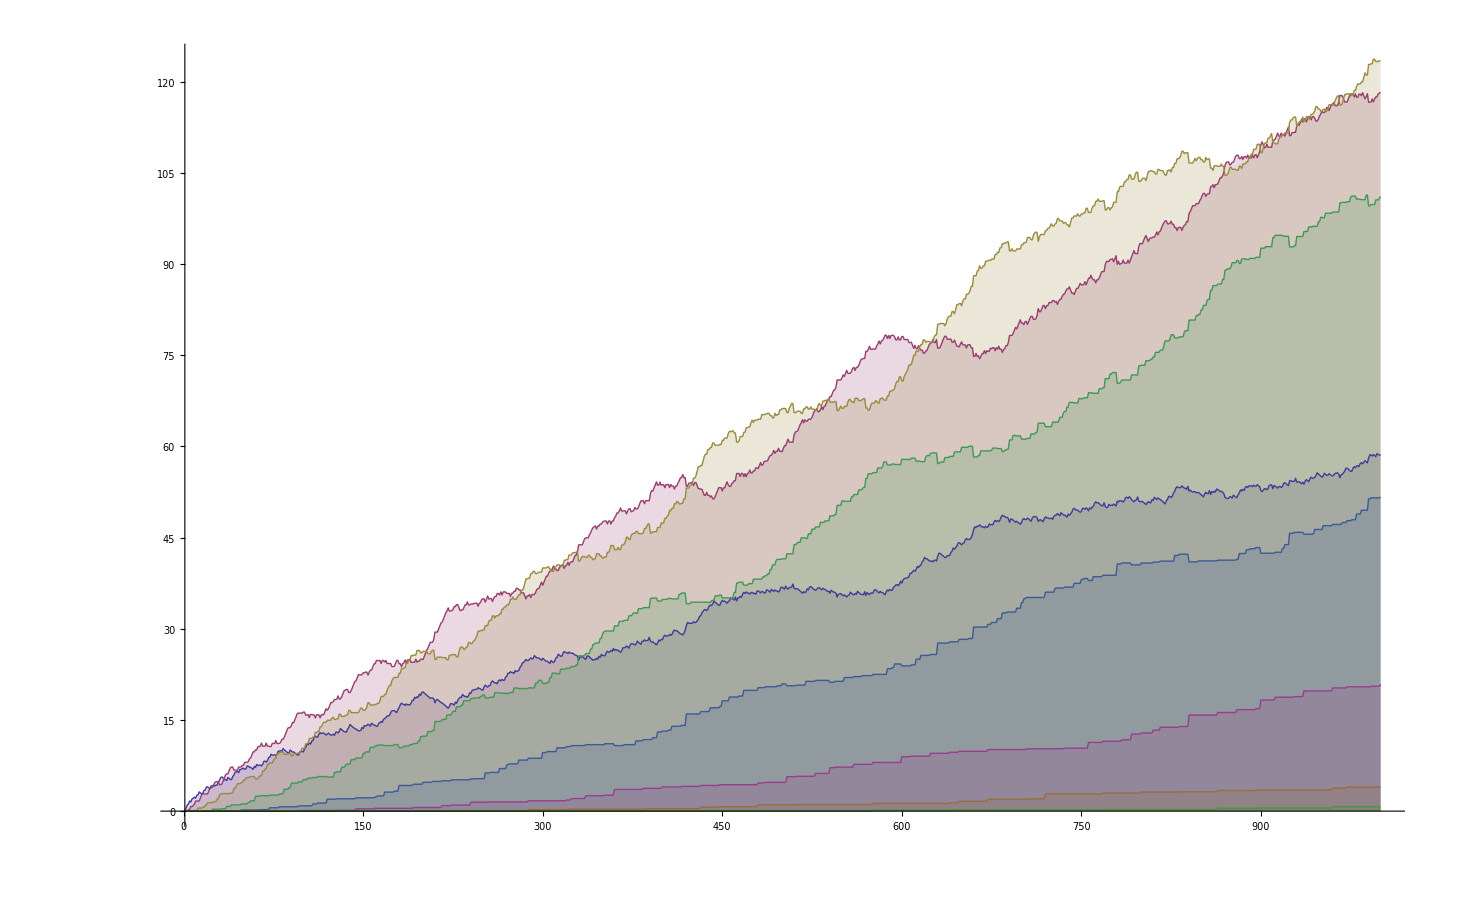

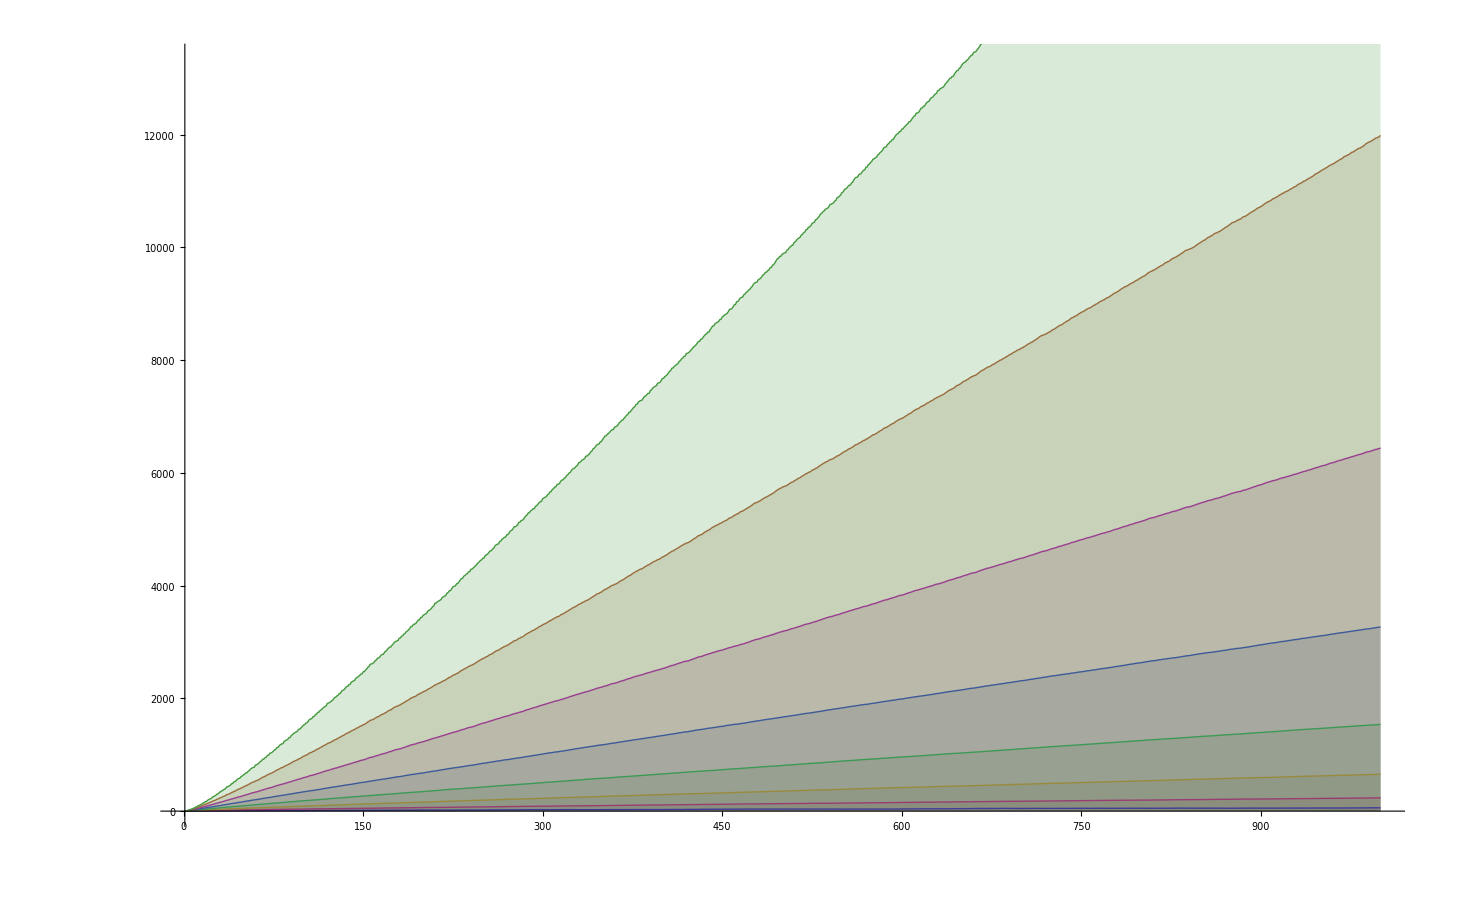

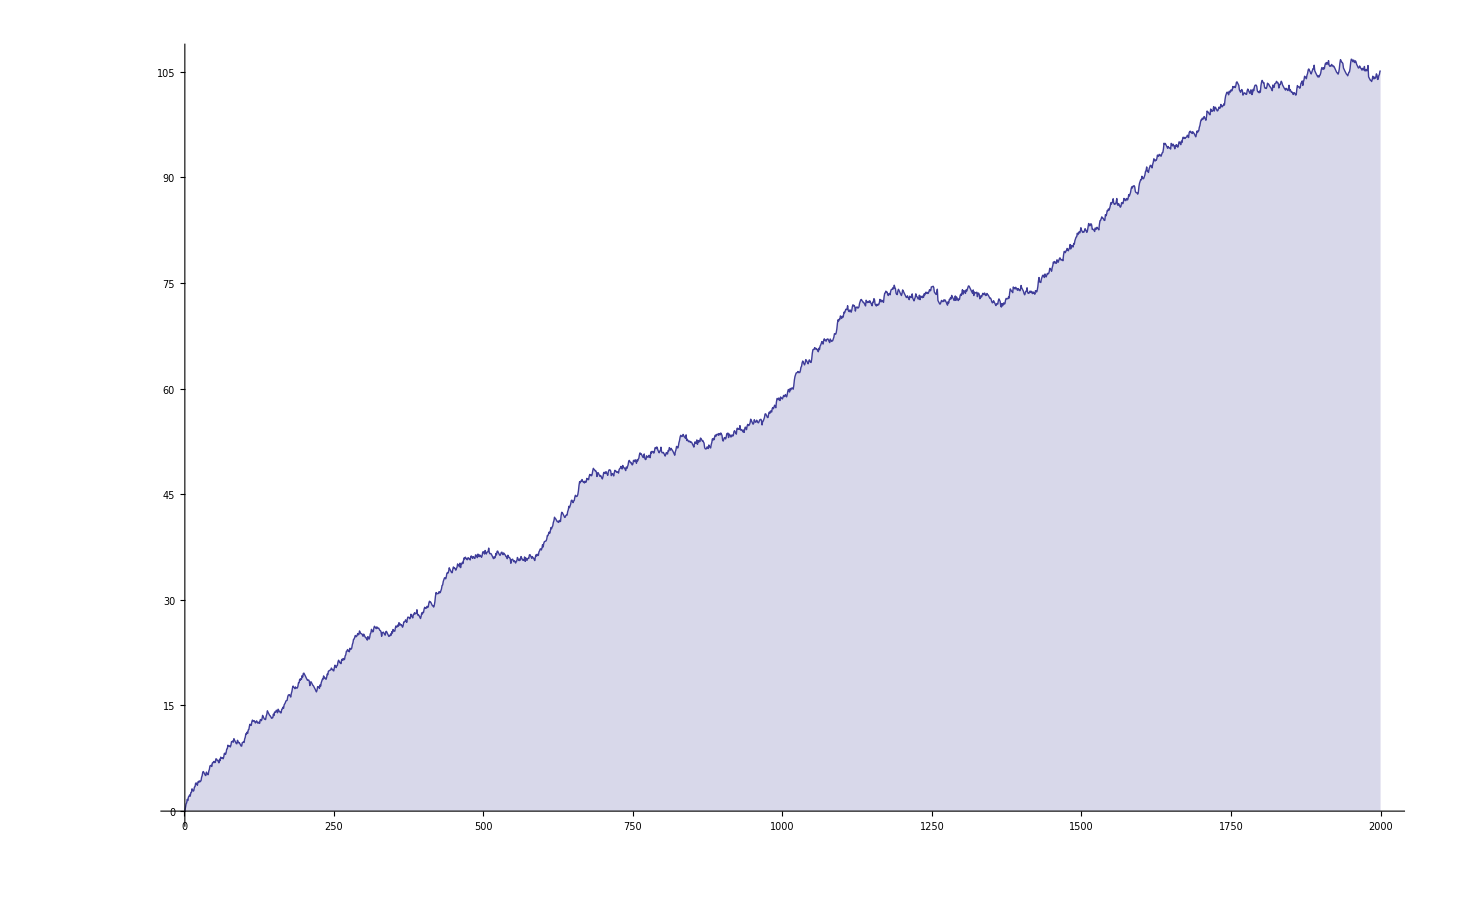

```mathematica
ClearAll["Global`*"]
d2[n_,k_]:=d2[n,k]=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1
D2[n_,k_]:=D2[n,k]=D2[n-1,k]+d2[n,k];D2[1,k_]:=0
K[n_]:=K[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
k2[n_,k_]:=k2[n,k]=Sum[k2[j,k-1] k2[n/j,1],{j,Divisors[n]}];k2[n_,1]:=K[n];k2[1,1]:=0;k2[n_,0]:=0;k2[1,0]:=1
K2[n_,k_]:=K2[n,k]=K2[n-1,k]+k2[n,k];K2[1,k_]:=0

cc:=cc=CoefficientList[Series[x/Log[1+x],{x,0,30}],x]
e2[n_,1]:=e2[n,1]=Sum[  cc[[k+1]] k2[n,k],{k,0,Log[2,n]}];e2[1,1]:=0;
e2[n_,k_]:=Sum[e2[j,k-1]e2[n/j,1],{j,Divisors[n]}];e2[n_,0]:=0;e2[1,0]:=1
E2[n_,k_] := E2[n,k] = E2[n-1,k]+e2[n,k];E2[1,k_]:=0
E1[n_,k_] := Sum[ Binomial[k,j] E2[n,j],{j,0,k}]
DiscretePlot[ {E2[n,1],E2[n,2],E2[n,3],E2[n,4],E2[n,5],E2[n,6],E2[n,7],E2[n,8]},{n,1,1000}]
DiscretePlot[ {E1[n,1],E1[n,2],E1[n,3],E1[n,4],E1[n,5],E1[n,6],E1[n,7],E1[n,8]},{n,1,1000}]
DiscretePlot[ {E1[n,1]},{n,1,2000}]
```

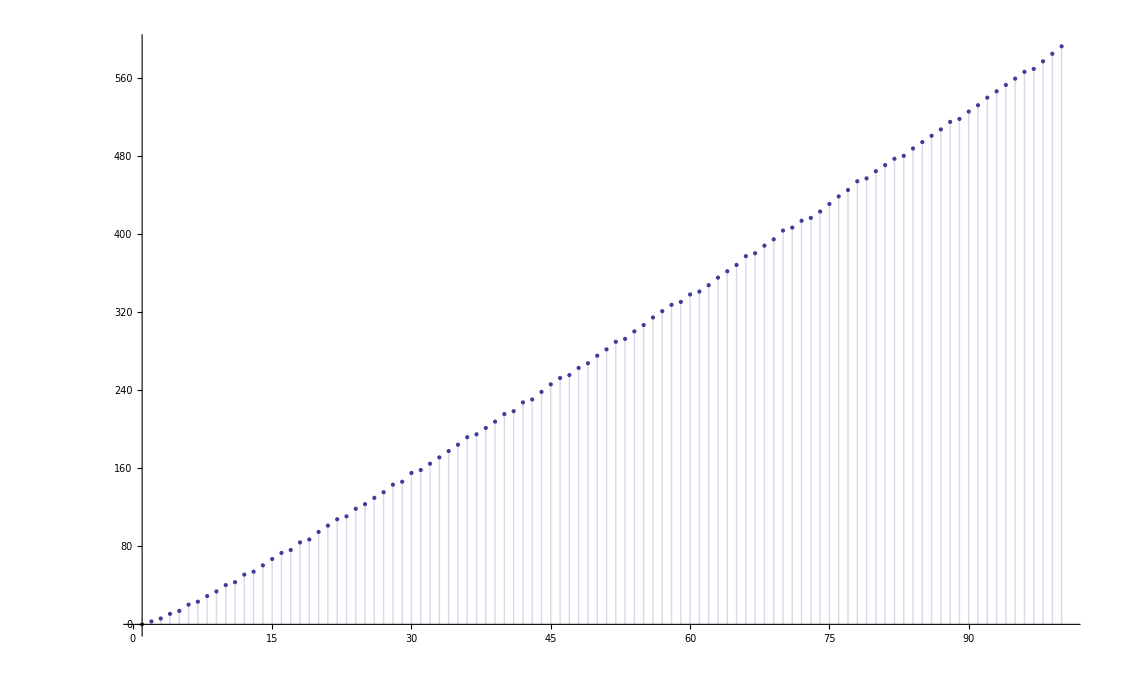

```mathematica
DiscretePlot[ {E1[n,6]},{n,1,100}]
```

```mathematica
Table[{n,E2[n,4]},{n,2,100}]//TableForm
```

2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0
11 | 0
12 | 0
13 | 0
14 | 0
15 | 0
16 | 1/16
17 | 1/16
18 | 1/16
19 | 1/16
20 | 1/16
21 | 1/16
22 | 1/16
23 | 1/16
24 | 5/16
25 | 5/16
26 | 5/16
27 | 5/16
28 | 5/16
29 | 5/16
30 | 5/16
31 | 5/16
32 | 19/48
33 | 19/48
34 | 19/48
35 | 19/48
36 | 37/48
37 | 37/48
38 | 37/48
39 | 37/48
40 | 49/48
41 | 49/48
42 | 49/48
43 | 49/48
44 | 49/48
45 | 49/48
46 | 49/48
47 | 49/48
48 | 19/16
49 | 19/16
50 | 19/16
51 | 19/16
52 | 19/16
53 | 19/16
54 | 23/16
55 | 23/16
56 | 27/16
57 | 27/16
58 | 27/16
59 | 27/16
60 | 39/16
61 | 39/16
62 | 39/16
63 | 39/16
64 | 61/24
65 | 61/24
66 | 61/24
67 | 61/24
68 | 61/24
69 | 61/24
70 | 61/24
71 | 61/24
72 | 21/8
73 | 21/8
74 | 21/8
75 | 21/8
76 | 21/8
77 | 21/8
78 | 21/8
79 | 21/8
80 | 67/24
81 | 137/48
82 | 137/48
83 | 137/48
84 | 173/48
85 | 173/48
86 | 173/48
87 | 173/48
88 | 185/48
89 | 185/48
90 | 221/48
91 | 221/48
92 | 221/48
93 | 221/48
94 | 221/48
95 | 221/48
96 | 77/16
97 | 77/16
98 | 77/16
99 | 77/16
100 | 83/16

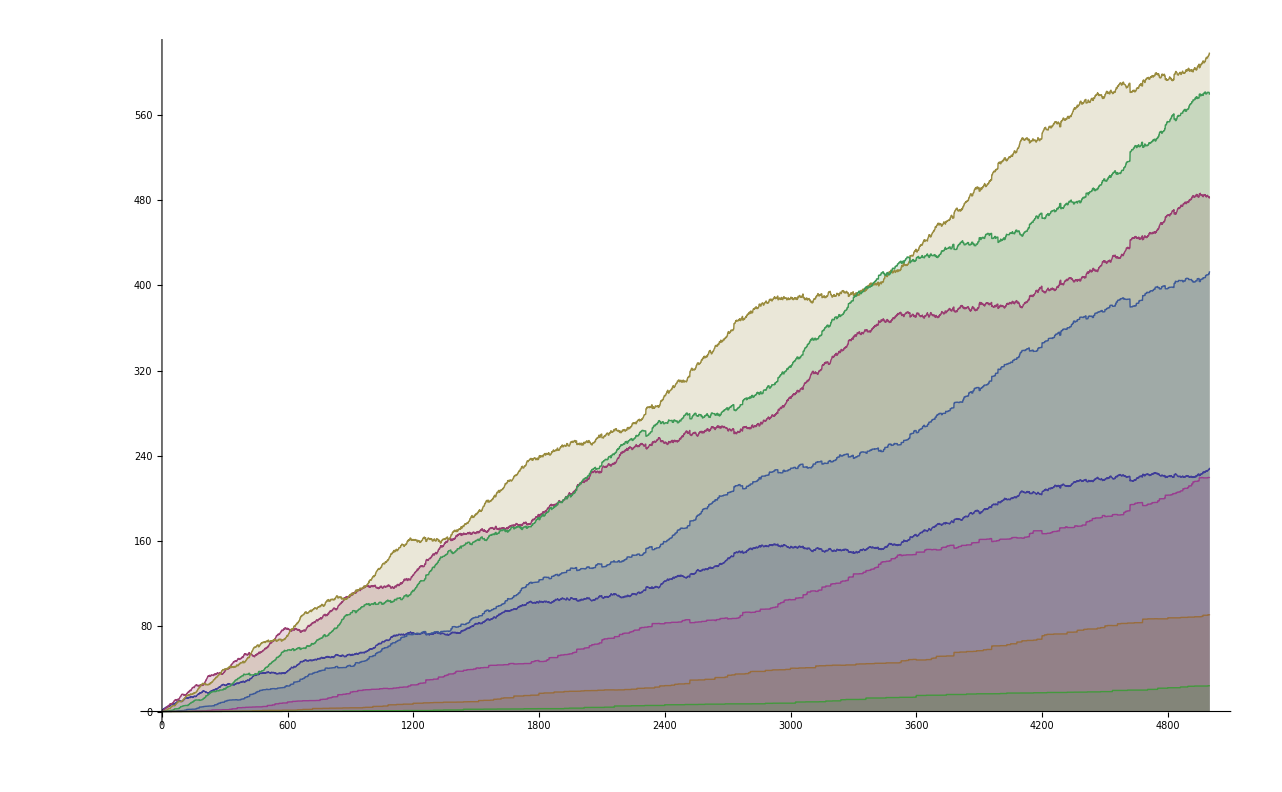

```mathematica
DiscretePlot[ {E2[n,1],E2[n,2],E2[n,3],E2[n,4],E2[n,5],E2[n,6],E2[n,7],E2[n,8]},{n,1,5000}]
```